```mathematica
Atree[{-Subscript[l, 1],-Subscript[l, 2],-Subscript[l, 3],Subscript[l, 4],Subscript[k, 3],Subscript[k, 4]}]//treesToLoops
```

dressTreeCO[{-l_1,-l_2,-l_3,l_4,k_3,k_4}]

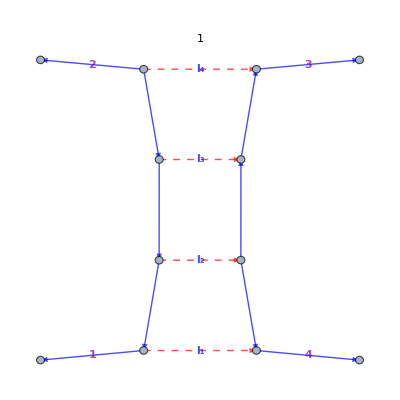
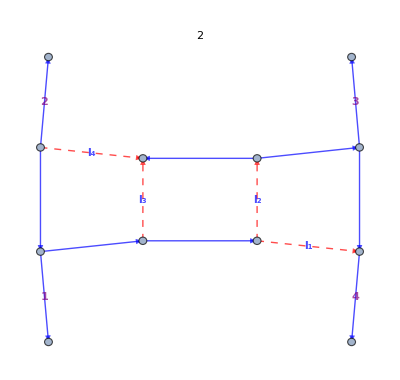
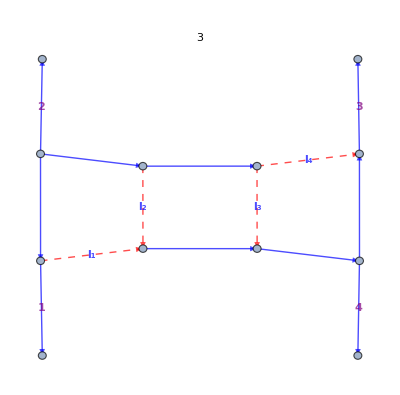
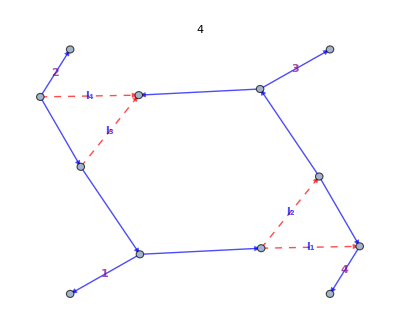
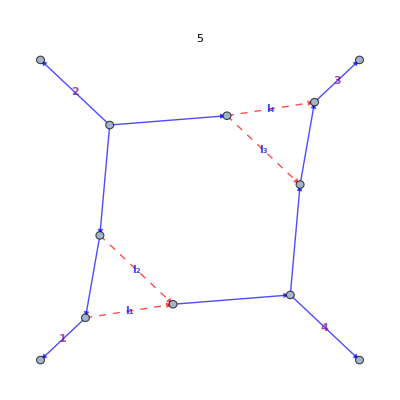
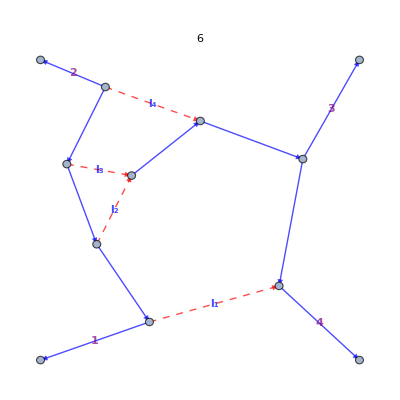
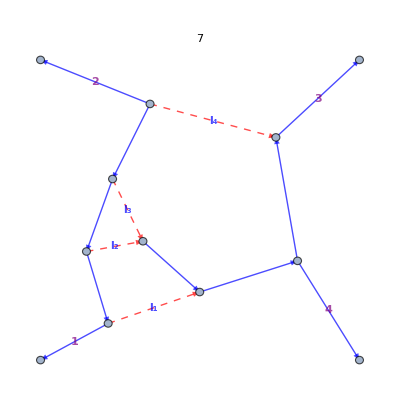
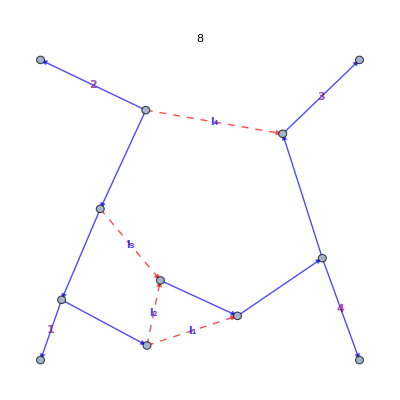
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MapIndexed[(doOrderedPlot[#,k/@Range[4],PlotLabel->#2[[1]]]//cutDisplayRule)&,allCutGraphsT]
```

```mathematica
treesToLoops[allCutsT[[1]]]
```

```mathematica
Table[treesToLoops[allCutsT[[i]]],{i,1,3}]//Flatten
```

```mathematica
sp=ResourceFunction["SetPartitions"][{a,b,c}]
```

{{{a,b,c}},{{a},{b,c}},{{a,b},{c}},{{a,c},{b}},{{a},{b},{c}}}

```mathematica
sp[[1]]
```

{{a,b,c}}

```mathematica
aaaa=ResourceFunction["SetPartitions"][{Atree[{k[1],in[12],in[8]}],
Atree[{k[2],in[5],-in[12]}],
Atree[{-in[5],in[6],in[9]}],
Atree[{-in[6],in[7],in[10]}],
Atree[{-in[10],in[14],in[11]}],
Atree[{-in[11],-in[8],-in[9]}],
 Atree[{-in[7],in[13],k[3]}],
 Atree[{-in[14],-in[13],k[4]}]}]
```

```mathematica
aaa[[1]][[1]]//toGraph// doOrderedPlot[#,k/@Range[4]]&
```

-Graphics-

```mathematica
sewGraphs[(aaa[[2]][[1]]//treesToLoops)[[1]],(aaa[[2]][[2]]//treesToLoops)[[1]]]//doOrderedPlot[#,k/@Range[4]]&
```

-Graphics-

```mathematica
aaa[[2]]//Flatten//ToString//StringCount[#,"in[6]"]&
```

2

```mathematica
fancyFormatOff
```

```mathematica
aaa[[2]]//Flatten//ToString
```

5                                                                    5                      5
{Atree[{l[-], in[12], in[8]}], Atree[{k[2], in[5], -in[12]}], Atree[{-in[5], l[-], in[9]}], Atree[{-l[-], in[7], in[10]}], Atree[{-in[10], in[14], in[11]}], Atree[{-in[11], -in[8], -in[9]}], Atree[{-in[7], in[13], k[3]}], Atree[{-in[14], -in[13], k[4]}]}
          2                                                                    2                      2

```mathematica
Cut[a__,ini__]:=
Module[ {n=a//Flatten//ToString//StringCount[#,"ini"]&,
nnnn=a//Flatten//ToString//StringCount[#,"l["]&
},
(nnnn+2)/2;
c=If[EvenQ[n],l[(nnnn+2)/2],ini];

b=a/.{ini->c}
]
```

```mathematica
l[1]
```

```mathematica
l[1]
```

```mathematica
aaaa[[2]]
```

{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}}

```mathematica
aaaa[[1]]
```

{{Atree[{k[1],in[12],in[8]}],Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}}

```mathematica
Cut[aaaa[[2]],in[5]]
```

{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],l[1],-in[12]}],Atree[{-l[1],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}}

```mathematica
{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],k[1],in[9]}],Atree[{-k[1],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}}
```

{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],k[1],in[9]}],Atree[{-k[1],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}}

```mathematica
Cut1[aaaa[[2]]]
```

{{Atree[{k[1],l[8],l[4]}]},{Atree[{k[2],l[1],-l[8]}],Atree[{-l[1],l[2],l[5]}],Atree[{-l[2],l[3],l[6]}],Atree[{-l[6],l[10],l[7]}],Atree[{-l[7],-l[4],-l[5]}],Atree[{-l[3],l[9],k[3]}],Atree[{-l[10],-l[9],k[4]}]}}

```mathematica
aaaa[[2]]
```

{{Atree[{k[1],in[12],in[8]}]},{Atree[{k[2],in[5],-in[12]}],Atree[{-in[5],in[6],in[9]}],Atree[{-in[6],in[7],in[10]}],Atree[{-in[10],in[14],in[11]}],Atree[{-in[11],-in[8],-in[9]}],Atree[{-in[7],in[13],k[3]}],Atree[{-in[14],-in[13],k[4]}]}}

```mathematica
l/:in=.
k[1]/:l[1]=.
```

TagUnset::tagnf: 在 in 中未找到标签 l.

```mathematica
in[6]
```

in[6]

```mathematica
k[1]/:l[1]=.
```

TagUnset::sym: 位置 1 处的参数 k[1] 应该是一个符号.

k[1]/:l[1]=.

```mathematica
ClearAll[k,l,aaaa]
```

```mathematica
Clear[k[1]]
```

Clear::ssym: k[1] 不是一个符号或者一个字符串.

```mathematica
k[1]
```

k[1]

```mathematica
Cut1[a__]:=
Map[Cut[a,#]&,Table[in[i],{i,1,30}]]
```

```mathematica
Cut1[a__]:=
For[i = 0, i < 30, i++, a=Cut[a,in[i]]];
a
```

a

```mathematica
Cut1[a__]:=
Module[{},
For[i = 0, i < 30, i++, a=Cut[a,in[i]]];
a
]
```

```mathematica
Remove[in,l,k]
```

```mathematica
aaaa[[2]]
```

{{A_3^tree(k_1,in[12],in[8])},{A_3^tree(k_2,in[5],-in[12]),A_3^tree(-in[5],in[6],in[9]),A_3^tree(-in[6],in[7],in[10]),A_3^tree(-in[10],in[14],in[11]),A_3^tree(-in[11],-in[8],-in[9]),A_3^tree(-in[7],in[13],k_3),A_3^tree(-in[14],-in[13],k_4)}}

```mathematica
Sew[aaaa[[2]]]
```

First::normal: First[d] 中的位置 1 处应该是非原子表达式.

Last::normal: Last[d] 中的位置 1 处应该是非原子表达式.

MapThread::mptd: MapThread[Style[#1,#3]&,{graphPlotForm[First[d]],graphPlotForm[Last[d]],graphPlotForm[color]}] 中位置 {2, 1} 处的对象 graphPlotForm[First[d]] 只含有 0 个维度（要求维度为 1）.

GraphPlot::graph: 在 GraphPlot[MapThread[Style[#1,#3]&,{graphPlotForm[First[d]],graphPlotForm[Last[d]],graphPlotForm[color]}],DirectedEdges→True,Method→{Spri…ding},«1»,VertexCoordinateRules→{neckl[{-k_(«1»)}]→{-0.707107,-0.707107},neckl[{-k_(«1»)}]→{-0.707107,0.707107},neckl[{-k_(«1»)}]→{0.707107,0.707107},neckl[{-k_(«1»)}]→{0.707107,-0.707107}},EdgeRenderingFunction→(Flatten[{If[labelHash$202710[«1»]===l,{Dashed,Red,Arrowheads[«1»],Thick,Arrow[«1»]},If[SameQ[«2»],{«3»},{«4»}]]}]&)] 中 中位置 1 处应该是一个图对象.

GraphPlot[MapThread[Style[#1#2,#3]&,{graphPlotForm[First[d]],graphPlotForm[Last[d]],graphPlotForm[RGBColor[0, 0, 1]]}],DirectedEdges→True,Method→{SpringElectricalEmbedding},MultiedgeStyle→0.5,VertexCoordinateRules→{neckl[{-k_1}]→{-0.707107,-0.707107},neckl[{-k_2}]→{-0.707107,0.707107},neckl[{-k_3}]→{0.707107,0.707107},neckl[{-k_4}]→{0.707107,-0.707107}},EdgeRenderingFunction→(Flatten[{If[labelHash$202710[#3/.a_b_c_:>a->b]===l,{Dashed,Red,Arrowheads[{{0.05,0.75}}],Thick,Arrow[#1]},If[labelHash$202710[#3/.a_b_c_:>a->b]===highlight,{RGBColor[0.074189364461738, 0.5290608072022583, 0.0075379568169680325],Thick,Arrow[#1]},{Blue,Arrowheads[1/18],Thick,Arrow[#1]}]]}]&)]

```mathematica
sewGraphs[(aaaa[[2]][[1]]//treesToLoops)[[1]],(aaaa[[2]][[2]]//treesToLoops)[[1]]]
```

vertexFormGraph[{neckl[{k_1,in[12],in[8]}],neckl[{k_2,in[5],-in[12]}],neckl[{-in[5],in[6],in[9]}],neckl[{-in[6],in[7],in[10]}],neckl[{-in[10],in[14],in[11]}],neckl[{-in[11],-in[8],-in[9]}],neckl[{-in[7],in[13],k_3}],neckl[{-in[14],-in[13],k_4}]}]

```mathematica
Length[aaaa[[2]]]
```

```mathematica
Sew1[b]
```

First::normal: First[d] 中的位置 1 处应该是非原子表达式.

Last::normal: Last[d] 中的位置 1 处应该是非原子表达式.

MapThread::mptd: MapThread[Style[#1,#3]&,{graphPlotForm[First[d]],graphPlotForm[Last[d]],graphPlotForm[color]}] 中位置 {2, 1} 处的对象 graphPlotForm[First[d]] 只含有 0 个维度（要求维度为 1）.

GraphPlot::graph: 在 GraphPlot[MapThread[Style[#1,#3]&,{graphPlotForm[First[d]],graphPlotForm[Last[d]],graphPlotForm[color]}],«4»,EdgeRenderingFunction→(Flatten[{If[labelHash$244633[«1»]===l,{Dashed,Red,«10»[«1»],Thick,Arrow[«1»]},If[SameQ[«2»],{«3»},{«4»}]]}]&)] 中 中位置 1 处应该是一个图对象.

GraphPlot[MapThread[Style[#1#2,#3]&,{graphPlotForm[First[d]],graphPlotForm[Last[d]],graphPlotForm[RGBColor[0, 0, 1]]}],DirectedEdges→True,Method→{SpringElectricalEmbedding},MultiedgeStyle→0.5,VertexCoordinateRules→{neckl[{-k_1}]→{-0.707107,-0.707107},neckl[{-k_2}]→{-0.707107,0.707107},neckl[{-k_3}]→{0.707107,0.707107},neckl[{-k_4}]→{0.707107,-0.707107}},EdgeRenderingFunction→(Flatten[{If[labelHash$244633[#3/.a_b_c_:>a->b]===l,{Dashed,Red,Arrowheads[{{0.05,0.75}}],Thick,Arrow[#1]},If[labelHash$244633[#3/.a_b_c_:>a->b]===highlight,{RGBColor[0.074189364461738, 0.5290608072022583, 0.0075379568169680325],Thick,Arrow[#1]},{Blue,Arrowheads[1/18],Thick,Arrow[#1]}]]}]&)]

```mathematica
sewGraphs[(b[[1]]//treesToLoops)[[1]],(b[[1+1]]//treesToLoops)[[1]]]//First
```

{neckl[{k_1,in[12],in[8]}],neckl[{k_2,in[5],-in[12]}],neckl[{-in[5],in[6],in[9]}],neckl[{-in[6],in[7],in[10]}],neckl[{-in[10],in[14],in[11]}],neckl[{-in[11],-in[8],-in[9]}],neckl[{-in[7],in[13],k_3}],neckl[{-in[14],-in[13],k_4}]}

```mathematica
For[i = 0, i < Length[aaaa[[2]]]-1, i++, d=sewGraphs[(b[[i+1]]//treesToLoops)[[1]],(b[[i+2]]//treesToLoops)[[1]]]];
d//doOrderedPlot[#,k/@Range[4]]&
```

-Graphics-

```mathematica
d
```

d

```mathematica
c
```

```mathematica
aaaa//Length
```

```mathematica
aaaa[[1]][[1]]
```

{A_3^tree(k_1,in[12],in[8]),A_3^tree(k_2,in[5],-in[12]),A_3^tree(-in[5],in[6],in[9]),A_3^tree(-in[6],in[7],in[10]),A_3^tree(-in[10],in[14],in[11]),A_3^tree(-in[11],-in[8],-in[9]),A_3^tree(-in[7],in[13],k_3),A_3^tree(-in[14],-in[13],k_4)}

```mathematica
Sew3[aaaa[[200]]]
```

-Graphics-

```mathematica
SewTest1[aaaa]
```

$Aborted

```mathematica
bbbbb=Table[aaaa[[i]],{i,1,10}]
```

{{{A_3^tree(k_1,in[12],in[8]),A_3^tree(k_2,in[5],-in[12]),A_3^tree(-in[5],in[6],in[9]),A_3^tree(-in[6],in[7],in[10]),A_3^tree(-in[10],in[14],in[11]),A_3^tree(-in[11],-in[8],-in[9]),A_3^tree(-in[7],in[13],k_3),A_3^tree(-in[14],-in[13],k_4)}},{{A_3^tree(k_1,in[12],in[8])},{A_3^tree(k_2,in[5],-in[12]),A_3^tree(-in[5],in[6],in[9]),A_3^tree(-in[6],in[7],in[10]),A_3^tree(-in[10],in[14],in[11]),A_3^tree(-in[11],-in[8],-in[9]),A_3^tree(-in[7],in[13],k_3),A_3^tree(-in[14],-in[13],k_4)}},{{A_3^tree(k_1,in[12],in[8]),A_3^tree(k_2,in[5],-in[12])},{A_3^tree(-in[5],in[6],in[9]),A_3^tree(-in[6],in[7],in[10]),A_3^tree(-in[10],in[14],in[11]),A_3^tree(-in[11],-in[8],-in[9]),A_3^tree(-in[7],in[13],k_3),A_3^tree(-in[14],-in[13],k_4)}},{{A_3^tree(k_1,in[12],in[8]),A_3^tree(-in[5],in[6],in[9]),A_3^tree(-in[6],in[7],in[10]),A_3^tree(-in[10],in[14],in[11]),A_3^tree(-in[11],-in[8],-in[9]),A_3^tree(-in[7],in[13],k_3),A_3^tree(-in[14],-in[13],k_4)},{A_3^tree(k_2,in[5],-in[12])}},{{A_3^tree(k_1,in[12],in[8]),A_3^tree(k_2,in[5],-in[12]),A_3^tree(-in[5],in[6],in[9])},{A_3^tree(-in[6],in[7],in[10]),A_3^tree(-in[10],in[14],in[11]),A_3^tree(-in[11],-in[8],-in[9]),A_3^tree(-in[7],in[13],k_3),A_3^tree(-in[14],-in[13],k_4)}},{{A_3^tree(k_1,in[12],in[8]),A_3^tree(-in[6],in[7],in[10]),A_3^tree(-in[10],in[14],in[11]),A_3^tree(-in[11],-in[8],-in[9]),A_3^tree(-in[7],in[13],k_3),A_3^tree(-in[14],-in[13],k_4)},{A_3^tree(k_2,in[5],-in[12]),A_3^tree(-in[5],in[6],in[9])}},{{A_3^tree(k_1,in[12],in[8]),A_3^tree(k_2,in[5],-in[12]),A_3^tree(-in[6],in[7],in[10]),A_3^tree(-in[10],in[14],in[11]),A_3^tree(-in[11],-in[8],-in[9]),A_3^tree(-in[7],in[13],k_3),A_3^tree(-in[14],-in[13],k_4)},{A_3^tree(-in[5],in[6],in[9])}},{{A_3^tree(k_1,in[12],in[8]),A_3^tree(-in[5],in[6],in[9])},{A_3^tree(k_2,in[5],-in[12]),A_3^tree(-in[6],in[7],in[10]),A_3^tree(-in[10],in[14],in[11]),A_3^tree(-in[11],-in[8],-in[9]),A_3^tree(-in[7],in[13],k_3),A_3^tree(-in[14],-in[13],k_4)}},{{A_3^tree(k_1,in[12],in[8]),A_3^tree(k_2,in[5],-in[12]),A_3^tree(-in[5],in[6],in[9]),A_3^tree(-in[6],in[7],in[10])},{A_3^tree(-in[10],in[14],in[11]),A_3^tree(-in[11],-in[8],-in[9]),A_3^tree(-in[7],in[13],k_3),A_3^tree(-in[14],-in[13],k_4)}},{{A_3^tree(k_1,in[12],in[8]),A_3^tree(-in[10],in[14],in[11]),A_3^tree(-in[11],-in[8],-in[9]),A_3^tree(-in[7],in[13],k_3),A_3^tree(-in[14],-in[13],k_4)},{A_3^tree(k_2,in[5],-in[12]),A_3^tree(-in[5],in[6],in[9]),A_3^tree(-in[6],in[7],in[10])}}}

```mathematica
SewTest1[bbbbb]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SewTest1[bbbbb][[1]]===SewTest1[bbbbb][[2]]
```

True

```mathematica
SewTest2[bbbbb]
```

{0,1,3,6,7}